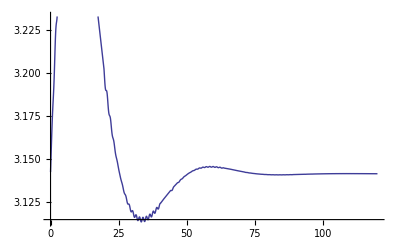

a.05.png

```mathematica
ClearSystemCache;
amp=.05; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=20*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;

Export["a.05.png",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```

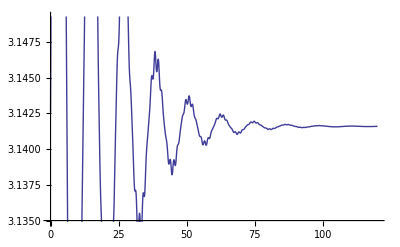

a.15.png

```mathematica
ClearSystemCache;
amp=.15; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=20*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;
Export["a.15.png",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```

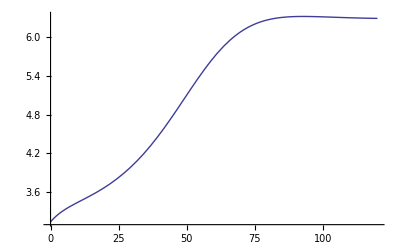

a.001.png

```mathematica
ClearSystemCache;
amp=.001; ω=5; mu=0.15;g=0.01;
DuffingForced={x'[t]==y[t],y'[t]==-Sin[x[t]](g+amp*ω*ω*Cos[ω*t])-mu*y[t]};
Plot[Evaluate[{x[t]}/.First[NDSolve[{DuffingForced,x[0]==Pi+0.001,y[0]==0.05},{x[t],y[t]},{t,0,150},StartingStepSize->0.001]]],{t,0,120}]
tmax=20*Pi;
AttractingWell[a_,b_]:=Sign[Abs[Mod[x[t],2*Pi]-Pi]-0.1]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;
Export["a.001.png",DensityPlot[AttractingWell[a,b],{a,0,2*Pi},{b,-Pi,Pi},MaxRecursion->3,Mesh->False,PlotPoints->130,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[0,2*Pi],Range[-Pi,Pi],None,None}]]
```